# Simulation of morphogen diffusion in narrow channels with binding

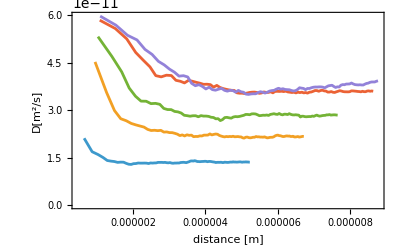

```mathematica
Clear["Global`*"] (* Clear all variables *)
SeedRandom[97];  (* set a fixed random seed for the simulations for reproducibility *)
(* With the parameters as given below the probram will run about 1 hour on a laptop*)

(* Simulation parameters *)
length=250 10^-6; (* channel length *)
 widthlist={ 0.5*10^-6,1*10^-6,1.5*10^-6,2.0*10^-6,2.5*10^-6}; (* channel halfwidth *)
dwidthlist = {2*10^-6,4*10^-6,6*10^-6,8*10^-6,10^-5}; (* width change over length of channel; >0 means a widening channel, <0 a narrowing channel; for constant channel width set all values in dwidthlist to 0; for converging channels set the values to negative ones; the lengths of the array needs to be the same as the length of widthlist *)
DiffCoeff=60 10^-12;(* Diffusion coefficient in m^2/s*)
timestep=0.01 10^-3; (* This should be set sufficiently small so that stepsize, defined in the next line is much smaller than the channel width to avoid artefacts *)
stepsize=Sqrt[2 DiffCoeff timestep]; (* mean squared displacement *)
numofiter=100000 ;(* number of steps in the simulation *) 
numofparticles=2000; (* number of particles to be simulated *)
totaltime=numofiter timestep; (* total simulation time *)
res=100; (* defines how often the diffusion coefficient will be calculated during the simulation; the final data will contain 'res' points *)
dreadout=Floor[numofiter/res]; (* number of timesteps after which the diffusion coefficient will be calculated *)
pbound=0.9; (* binding probability of ligand to receptor when membrane is hit *)
punbound=0.01; (* unbinding probability of ligand from receptor *)

(* Module to calculate the encounter position on the channel border if a particle hits it during a timestep *)
(* This defines the position on the border if a particle binds. *)
(* To avoid rare issues of calcualtion precision and divisions by zero the program checks for correct positions *)
impactPoint[x_,y_,dx_,dy_,pbu_,pbl_,s_,w_]:=
Module[{a=dy/dx,c=(y-(dy/dx) x),b=Sign[x] (pbu-pbl) s,d=(pbu-pbl) w,tmp},
tmp=(d-c)/(a-b);
If[Abs[tmp-x]>Abs[dx] &&Abs[a tmp+c-y]>Abs[dy],
{(x+b (y-d))/(1+b^2),(b x+(b^2 y+d))/(1+b^2)},
{tmp,a tmp+c}]];

(* Module to calculate the position after reflection at border if a particle hits it during a timestep *)
(* pr is the impact point; dx/dy are the random displacements in that timestep; dw/dl defines the normal vector on the border*)
reflection[pr_,dx_,dy_,dw_,dl_]:= 
Module[{refl,signw,signl},
signl=Sign[pr[[1]]];
signw=Sign[pr[[2]]];
refl=ReflectionTransform[{-signw dw,signl dl}][{dx,dy}]; (* {-dw, dl} is the normal vector on the border *)
pr+refl];

(* Result tables *)
arraylength=Length[widthlist]; (* calculate how many simulations are to be run based on the user input in widthlist *)
Dapp=Table[0,{res}]; (* apparent diffusion coefficient calculated for different positions and times *)
msd=Table[0,{res}];(* distance at which D was calculated; this will be given by the MSD *)
sqrtmsd=Table[0,{arraylength}];
dataspace=Table[0,{arraylength}];(* Array containing the data for the D plots; each simulation has 'res' points  *)

For[k=1,k≤ arraylength,k++,
width=widthlist[[k]]; (* running for different channel width as defined in widthlist *)
dwidth=dwidthlist[[k]];
slope=dwidth/length;
bu[x_]:=width+slope x/;x>=0 ;(* upper border of channel *)
bu[x_]:=width-slope x/;x<0;
bl[x_]:=-bu[x] ;(* lower border of channel *)
px=Table[0,{numofparticles}]; (* x-coordinate of particles *)
py=Table[0,{numofparticles}];(* y-coordinate of particles *)
pm=Table[1,{numofparticles}]; (* mobility of particle: 1=mobile; 0=immobile/bound *)
counter=1; (* set the counter for the recording of apparent D values *)
For[iter=1,iter<=numofiter,iter+=1, (* run through the iterations *)
dpx=RandomVariate[NormalDistribution[0,stepsize],numofparticles]; (* x displacement *)
dpy=RandomVariate[NormalDistribution[0,stepsize],numofparticles]; (* y displacement *)
pm=Ceiling[(pm+RandomVariate[BernoulliDistribution[punbound],numofparticles])/2]; (* update mobility if particle will unbind; logical or *)
px+=dpx*pm; (* new x-coordinates *)
py+=dpy*pm;(* new y-coordinates *)
bul=Table[bu[px[[i]]],{i,1,numofparticles}]; (* upper channel limits at these new x-coordinates *)
bll=-bul; (* lower channel limits at these new x-coordinates *)
pbu=(GreaterEqualThan[0]/@(py-bul))/.{True->1,False->0}; (* did particle move across upper border? *)
pbl=(LessThan[0]/@(py-bll))/.{True->1,False->0}; (* did particle move across lower border? *)
pb=RandomVariate[BernoulliDistribution[pbound],numofparticles]; (* If it moved over channel border did it bind? *)
pm*=(1-(pbu+pbl)*pb); (* update mobility *)
Do[ (* determine for each particle that went over the border whether it is reflected or bound *)
If[(pbu[[i]]+pbl[[i]])==1, (* if the particle went over a channel border *)
{ipoint=impactPoint[px[[i]],py[[i]],dpx[[i]],dpy[[i]],pbu[[i]],pbl[[i]],slope,width], (* define the exact point where the crossing happens *)
If[pm[[i]]==0 , (* if the particle was bound ... *)
{px[[i]]=ipoint[[1]],py[[i]]=ipoint[[2]]}, (* ... determine the point where it was bound *)
{ptmp=reflection[ipoint,dpx[[i]],dpy[[i]],dwidth,length],px[[i]]=ptmp[[1]],py[[i]]=ptmp[[2]]}]}], (* otherwise determine where it was reflected to *)
{i,1,numofparticles}];
If[Mod[iter,dreadout]==0,(* D will be calculated only every 'dreadout' steps and the data will be saved *)
{Dapp[[counter]]=Variance[px]/(2 iter timestep), (* calculate D from positional variance *)
msd[[counter]]=2*Dapp[[counter]]*timestep*(numofiter/res);(* calculate the mean squared displacements *)
(*Alternatively, the mean squared displacement can be calculated directly from the variance *)
(*distance[[counter]]=Sqrt[Variance[px]];*)
counter++}
] 
];
sqrtmsd=Sqrt[Accumulate[msd]];
dataspace[[k]]=Transpose[{sqrtmsd,Dapp}] (* store the data of D as function of space *)
];

(* If desired, the data can be saved; for that purpose, remove the comment markers of the following commands, insert your directory path for "/..." for saving and change the filename in "filename.dat" to the desired name: *) 

(*SetDirectory["/..."];
Save["filename.dat",{dataspace,pxlist}]*)

(* Plot D as function of space and time *)
ListPlot[dataspace,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"distance [m]",Rotate["D[m^2/s]",-90 Degree]}]
```